```mathematica
Mixing (one res, one bound)
```

## DEFINE PARAMTERS

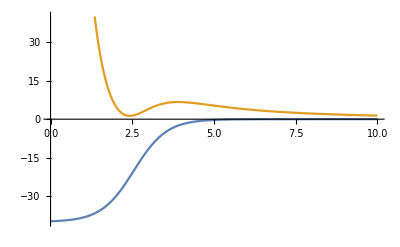

```mathematica
Subscript[m, N]=940;ℏc=197.327;
V0=40;R=2.55;a=0.5;μ=8/9 Subscript[m, N];
E2=3;
rmax=10.;dr=0.01;
rlist=Range[dr,rmax,dr];
len=Length[rlist];
Vwoods[r_]:=-V0/(1+Exp[(r-R)/a]);
Vcent[r_,l_]:=(l(l+1)ℏc^2)/(2μ r^2);
V00[r_]:=Vwoods[r]+Vcent[r,0];
V22[r_]:=Vwoods[r]+Vcent[r,2];
V00mat:=DiagonalMatrix[V00[rlist]];
V22mat:=DiagonalMatrix[V22[rlist]];
(*MIXING*)
V02mat:=DiagonalMatrix[Vwoods[rlist]];
V20mat:=DiagonalMatrix[Vwoods[rlist]];
(*INITIAL HAMILTONIAN*)
one[n_,d_]:=
DiagonalMatrix[1+0Range[n-Abs[d]],d];
H000:=V00mat+-ℏc^2/(2 μ) 1/dr^2(one[len,-1]-2 one[len,0]+one[len,1]);
H022:=V22mat+-ℏc^2/(2 μ) 1/dr^2(one[len,-1]-2 one[len,0]+one[len,1])+E2;
H0:=ArrayFlatten[{{H000,V02mat},{V20mat,H022}}];
ListLinePlot[{V00[rlist],V22[rlist]},DataRange->{dr,rmax},PlotRange->{-V0,V0}]
```

## SOLUTIONS

```mathematica
(*DEFINITIONS*)
```

```mathematica
k0[En_?NumericQ]:=Sqrt[(2μ En)/ℏc^2];
k2[En_?NumericQ]:=Sqrt[(2μ (En-E2))/ℏc^2];
wave0[En_,r_]:=SphericalHankelH1[0,k0[En] r];
wave2[En_,r_]:=SphericalHankelH1[2,k2[En] r];
B0[En_]:=rmax/wave0[En,rmax](D[wave0[En,r],r]/.r->rmax);
B2[En_]:=rmax/wave2[En,rmax](D[wave2[En,r],r]/.r->rmax);
(*HAMILTONIAN*)
Hnew[En_]:=Module[{H=H0},H[[len,len]]=V00mat[[len,len]]+-ℏc^2/(2 μ) 1/dr^2(dr B0[En]/rmax-1);H[[2 len,2 len]]=V22mat[[len,len]]+-ℏc^2/(2 μ) 1/dr^2(dr B2[En]/rmax-1);H];
(*RETURNS EIGEMVALUE*)
ϵ=10^-10;
n=2;
evals=List[];evecs=List[];
eigenv[{En_?NumericQ,i_}]:=({eval,evec}=Transpose@SortBy[Transpose[Eigensystem[Hnew[En]]],First];{eval[[i]],i});
```

```mathematica
(*RETURNS EIGENSYSTEM*)
(*En=x/.FindRoot[Im[eigenvres1[x,n,l]]==Im[x],{x,0.1+0.I,0.,V0}]//Timing*)
res=NestWhileList[eigenv,{0.,n},Abs[Abs[#1[[1]]]-Abs[#2[[1]]]]>ϵ&,2,40];
evals=Append[evals,En];evecs=Append[evecs,evec[[n]]];
```

```mathematica
res48
```

{{-24,2},{1.00933+0. ⅈ,2},{0.55156-0.362694 ⅈ,2},{0.314677-0.342157 ⅈ,2},{0.247564-0.297942 ⅈ,2},{0.233263-0.269747 ⅈ,2},{0.23433-0.256655 ⅈ,2},{0.237704-0.252268 ⅈ,2},{0.239911-0.251515 ⅈ,2},{0.240856-0.251768 ⅈ,2},{0.241126-0.252077 ⅈ,2},{0.241148-0.252248 ⅈ,2},{0.241116-0.252312 ⅈ,2},{0.24109-0.252327 ⅈ,2},{0.241077-0.252326 ⅈ,2},{0.241073-0.252323 ⅈ,2},{0.241072-0.252321 ⅈ,2},{0.241073-0.25232 ⅈ,2},{0.241073-0.25232 ⅈ,2},{0.241073-0.25232 ⅈ,2},{0.241073-0.25232 ⅈ,2},{0.241073-0.25232 ⅈ,2},{0.241073-0.25232 ⅈ,2},{0.241073-0.25232 ⅈ,2},{0.241073-0.25232 ⅈ,2},{0.241073-0.25232 ⅈ,2},{0.241073-0.25232 ⅈ,2},{0.241073-0.25232 ⅈ,2},{0.241073-0.25232 ⅈ,2},{0.241073-0.25232 ⅈ,2},{0.241073-0.25232 ⅈ,2},{0.241073-0.25232 ⅈ,2},{0.241073-0.25232 ⅈ,2},{0.241073-0.25232 ⅈ,2},{0.241073-0.25232 ⅈ,2},{0.241073-0.25232 ⅈ,2},{0.241073-0.25232 ⅈ,2}}

```mathematica
V0=47;res47=NestWhileList[eigenv,{0.,n},Abs[Abs[#1[[1]]]-Abs[#2[[1]]]]>ϵ&,2,40]
```

{{0.,2},{0.220878+0. ⅈ,2},{0.55996-0.218766 ⅈ,2},{0.501085-0.349833 ⅈ,2},{0.459709-0.376119 ⅈ,2},{0.442081-0.376955 ⅈ,2},{0.436236-0.374059 ⅈ,2},{0.434855-0.37205 ⅈ,2},{0.434771-0.371141 ⅈ,2},{0.434911-0.370828 ⅈ,2},{0.435014-0.370751 ⅈ,2},{0.435062-0.370745 ⅈ,2},{0.435079-0.370752 ⅈ,2},{0.435083-0.370758 ⅈ,2},{0.435084-0.37076 ⅈ,2},{0.435083-0.370761 ⅈ,2},{0.435083-0.370761 ⅈ,2},{0.435083-0.370761 ⅈ,2},{0.435083-0.370761 ⅈ,2},{0.435083-0.370761 ⅈ,2},{0.435083-0.370761 ⅈ,2},{0.435083-0.370761 ⅈ,2},{0.435083-0.370761 ⅈ,2},{0.435083-0.370761 ⅈ,2},{0.435083-0.370761 ⅈ,2},{0.435083-0.370761 ⅈ,2},{0.435083-0.370761 ⅈ,2}}

```mathematica
V0=46;res46=NestWhileList[eigenv,{0.,n},Abs[Abs[#1[[1]]]-Abs[#2[[1]]]]>ϵ&,2,40]
```

{{0.,2},{0.312269+0. ⅈ,2},{0.69841-0.281167 ⅈ,2},{0.663464-0.436006 ⅈ,2},{0.627079-0.474838 ⅈ,2},{0.609678-0.481252 ⅈ,2},{0.603107-0.48061 ⅈ,2},{0.601081-0.479377 ⅈ,2},{0.600617-0.47866 ⅈ,2},{0.60058-0.478355 ⅈ,2},{0.600615-0.47825 ⅈ,2},{0.600643-0.478221 ⅈ,2},{0.600657-0.478216 ⅈ,2},{0.600662-0.478217 ⅈ,2},{0.600664-0.478218 ⅈ,2},{0.600664-0.478218 ⅈ,2},{0.600664-0.478219 ⅈ,2},{0.600664-0.478219 ⅈ,2},{0.600664-0.478219 ⅈ,2},{0.600664-0.478219 ⅈ,2},{0.600664-0.478219 ⅈ,2},{0.600664-0.478219 ⅈ,2},{0.600664-0.478219 ⅈ,2},{0.600664-0.478219 ⅈ,2},{0.600664-0.478219 ⅈ,2},{0.600664-0.478219 ⅈ,2},{0.600664-0.478219 ⅈ,2},{0.600664-0.478219 ⅈ,2}}

```mathematica
V0=45;res45=NestWhileList[eigenv,{0.,n},Abs[Abs[#1[[1]]]-Abs[#2[[1]]]]>ϵ&,2,40]
```

{{0.,2},{0.390043+0. ⅈ,2},{0.818726-0.335906 ⅈ,2},{0.803199-0.516409 ⅈ,2},{0.770008-0.567134 ⅈ,2},{0.752376-0.578402 ⅈ,2},{0.745113-0.579597 ⅈ,2},{0.742577-0.578978 ⅈ,2},{0.741833-0.578421 ⅈ,2},{0.741667-0.578135 ⅈ,2},{0.741652-0.578018 ⅈ,2},{0.741664-0.577977 ⅈ,2},{0.741674-0.577966 ⅈ,2},{0.741678-0.577963 ⅈ,2},{0.74168-0.577963 ⅈ,2},{0.741681-0.577963 ⅈ,2},{0.741681-0.577964 ⅈ,2},{0.741681-0.577964 ⅈ,2},{0.741681-0.577964 ⅈ,2},{0.741681-0.577964 ⅈ,2},{0.741681-0.577964 ⅈ,2},{0.741681-0.577964 ⅈ,2},{0.741681-0.577964 ⅈ,2},{0.741681-0.577964 ⅈ,2},{0.741681-0.577964 ⅈ,2}}

```mathematica
V0=44;res44=NestWhileList[eigenv,{0.,n},Abs[Abs[#1[[1]]]-Abs[#2[[1]]]]>ϵ&,2,40]
```

{{0.,2},{0.456967+0. ⅈ,2},{0.923871-0.385018 ⅈ,2},{0.923552-0.591111 ⅈ,2},{0.892352-0.653006 ⅈ,2},{0.874254-0.668704 ⅈ,2},{0.866319-0.671553 ⅈ,2},{0.863327-0.671491 ⅈ,2},{0.862341-0.671089 ⅈ,2},{0.862063-0.67083 ⅈ,2},{0.862004-0.670708 ⅈ,2},{0.862-0.67066 ⅈ,2},{0.862005-0.670644 ⅈ,2},{0.862008-0.670639 ⅈ,2},{0.86201-0.670638 ⅈ,2},{0.862011-0.670637 ⅈ,2},{0.862011-0.670637 ⅈ,2},{0.862011-0.670637 ⅈ,2},{0.862011-0.670638 ⅈ,2},{0.862011-0.670638 ⅈ,2},{0.862011-0.670638 ⅈ,2},{0.862011-0.670638 ⅈ,2},{0.862011-0.670638 ⅈ,2},{0.862011-0.670638 ⅈ,2},{0.862011-0.670638 ⅈ,2},{0.862011-0.670638 ⅈ,2},{0.862011-0.670638 ⅈ,2},{0.862011-0.670638 ⅈ,2},{0.862011-0.670638 ⅈ,2},{0.862011-0.670638 ⅈ,2},{0.862011-0.670638 ⅈ,2},{0.862011-0.670638 ⅈ,2},{0.862011-0.670638 ⅈ,2},{0.862011-0.670638 ⅈ,2},{0.862011-0.670638 ⅈ,2}}

```mathematica
V0=43;res43=NestWhileList[eigenv,{0.,n},Abs[Abs[#1[[1]]]-Abs[#2[[1]]]]>ϵ&,2,40]
```

{{0.,2},{0.51521+0. ⅈ,2},{1.01641-0.429538 ⅈ,2},{1.02776-0.660187 ⅈ,2},{0.997685-0.732515 ⅈ,2},{0.978966-0.752337 ⅈ,2},{0.970365-0.756737 ⅈ,2},{0.966945-0.757208 ⅈ,2},{0.965732-0.756964 ⅈ,2},{0.965349-0.756737 ⅈ,2},{0.965246-0.756616 ⅈ,2},{0.965226-0.756562 ⅈ,2},{0.965225-0.756541 ⅈ,2},{0.965227-0.756534 ⅈ,2},{0.965229-0.756532 ⅈ,2},{0.96523-0.756532 ⅈ,2},{0.96523-0.756532 ⅈ,2},{0.96523-0.756532 ⅈ,2},{0.96523-0.756532 ⅈ,2},{0.96523-0.756532 ⅈ,2},{0.96523-0.756532 ⅈ,2},{0.96523-0.756532 ⅈ,2},{0.96523-0.756532 ⅈ,2},{0.96523-0.756532 ⅈ,2},{0.96523-0.756532 ⅈ,2},{0.96523-0.756532 ⅈ,2},{0.96523-0.756532 ⅈ,2},{0.96523-0.756532 ⅈ,2},{0.96523-0.756532 ⅈ,2},{0.96523-0.756532 ⅈ,2},{0.96523-0.756532 ⅈ,2},{0.96523-0.756532 ⅈ,2},{0.96523-0.756532 ⅈ,2},{0.96523-0.756532 ⅈ,2},{0.96523-0.756532 ⅈ,2},{0.96523-0.756532 ⅈ,2},{0.96523-0.756532 ⅈ,2},{0.96523-0.756532 ⅈ,2},{0.96523-0.756532 ⅈ,2},{0.96523-0.756532 ⅈ,2},{0.96523-0.756532 ⅈ,2}}

```mathematica
V0=42;res42=NestWhileList[eigenv,{0.,n},Abs[Abs[#1[[1]]]-Abs[#2[[1]]]]>ϵ&,2,40]
```

{{0.,2},{0.566478+0. ⅈ,2},{1.09851-0.470162 ⅈ,2},{1.11871-0.7239 ⅈ,2},{1.08911-0.805946 ⅈ,2},{1.06966-0.829642 ⅈ,2},{1.06039-0.835521 ⅈ,2},{1.05655-0.836512 ⅈ,2},{1.05512-0.836428 ⅈ,2},{1.05463-0.836239 ⅈ,2},{1.05448-0.83612 ⅈ,2},{1.05445-0.836063 ⅈ,2},{1.05444-0.836039 ⅈ,2},{1.05444-0.83603 ⅈ,2},{1.05444-0.836027 ⅈ,2},{1.05444-0.836026 ⅈ,2},{1.05444-0.836025 ⅈ,2},{1.05444-0.836025 ⅈ,2},{1.05444-0.836025 ⅈ,2},{1.05444-0.836025 ⅈ,2},{1.05444-0.836025 ⅈ,2},{1.05444-0.836025 ⅈ,2},{1.05444-0.836025 ⅈ,2},{1.05444-0.836025 ⅈ,2},{1.05444-0.836025 ⅈ,2},{1.05444-0.836025 ⅈ,2}}

```mathematica
V0=41;res41=NestWhileList[eigenv,{0.,n},Abs[Abs[#1[[1]]]-Abs[#2[[1]]]]>ϵ&,2,40]
```

{{0.,2},{0.61211+0. ⅈ,2},{1.17199-0.50744 ⅈ,2},{1.19883-0.782666 ⅈ,2},{1.16924-0.873758 ⅈ,2},{1.14895-0.90111 ⅈ,2},{1.139-0.908407 ⅈ,2},{1.13475-0.909908 ⅈ,2},{1.1331-0.909986 ⅈ,2},{1.13251-0.909839 ⅈ,2},{1.13232-0.909725 ⅈ,2},{1.13226-0.909664 ⅈ,2},{1.13225-0.909637 ⅈ,2},{1.13225-0.909626 ⅈ,2},{1.13225-0.909622 ⅈ,2},{1.13225-0.909621 ⅈ,2},{1.13225-0.90962 ⅈ,2},{1.13225-0.90962 ⅈ,2},{1.13225-0.90962 ⅈ,2},{1.13225-0.90962 ⅈ,2},{1.13225-0.90962 ⅈ,2},{1.13225-0.90962 ⅈ,2},{1.13225-0.90962 ⅈ,2},{1.13225-0.90962 ⅈ,2},{1.13225-0.90962 ⅈ,2},{1.13225-0.90962 ⅈ,2}}

```mathematica
V0=40;res40=NestWhileList[eigenv,{0.,n},Abs[Abs[#1[[1]]]-Abs[#2[[1]]]]>ϵ&,2,40]
```

{{0.,2},{0.653168+0. ⅈ,2},{1.23833-0.541839 ⅈ,2},{1.27014-0.836984 ⅈ,2},{1.24018-0.936508 ⅈ,2},{1.21898-0.967318 ⅈ,2},{1.20835-0.975975 ⅈ,2},{1.20368-0.977975 ⅈ,2},{1.20181-0.978215 ⅈ,2},{1.20112-0.978111 ⅈ,2},{1.20088-0.978004 ⅈ,2},{1.2008-0.977941 ⅈ,2},{1.20078-0.977911 ⅈ,2},{1.20078-0.977898 ⅈ,2},{1.20078-0.977893 ⅈ,2},{1.20078-0.977891 ⅈ,2},{1.20078-0.97789 ⅈ,2},{1.20078-0.97789 ⅈ,2},{1.20078-0.97789 ⅈ,2},{1.20078-0.97789 ⅈ,2},{1.20078-0.97789 ⅈ,2},{1.20078-0.97789 ⅈ,2},{1.20078-0.97789 ⅈ,2},{1.20078-0.97789 ⅈ,2},{1.20078-0.97789 ⅈ,2},{1.20078-0.97789 ⅈ,2},{1.20078-0.97789 ⅈ,2},{1.20078-0.97789 ⅈ,2},{1.20078-0.97789 ⅈ,2},{1.20078-0.97789 ⅈ,2},{1.20078-0.97789 ⅈ,2},{1.20078-0.97789 ⅈ,2},{1.20078-0.97789 ⅈ,2}}

```mathematica
V0=39;res39=NestWhileList[eigenv,{0.,n},Abs[Abs[#1[[1]]]-Abs[#2[[1]]]]>ϵ&,2,40]
```

{{0.,2},{0.690501+0. ⅈ,2},{1.29879-0.573768 ⅈ,2},{1.33427-0.887381 ⅈ,2},{1.30367-0.994784 ⅈ,2},{1.2815-1.02886 ⅈ,2},{1.27016-1.03883 ⅈ,2},{1.26508-1.04131 ⅈ,2},{1.26299-1.04171 ⅈ,2},{1.26219-1.04165 ⅈ,2},{1.2619-1.04155 ⅈ,2},{1.26181-1.04149 ⅈ,2},{1.26178-1.04145 ⅈ,2},{1.26177-1.04144 ⅈ,2},{1.26177-1.04143 ⅈ,2},{1.26177-1.04143 ⅈ,2},{1.26177-1.04143 ⅈ,2},{1.26177-1.04143 ⅈ,2},{1.26177-1.04143 ⅈ,2},{1.26177-1.04143 ⅈ,2},{1.26177-1.04143 ⅈ,2},{1.26177-1.04143 ⅈ,2},{1.26177-1.04143 ⅈ,2},{1.26177-1.04143 ⅈ,2},{1.26177-1.04143 ⅈ,2},{1.26177-1.04143 ⅈ,2},{1.26177-1.04143 ⅈ,2},{1.26177-1.04143 ⅈ,2},{1.26177-1.04143 ⅈ,2},{1.26177-1.04143 ⅈ,2},{1.26177-1.04143 ⅈ,2}}

```mathematica
V0=38;res38=NestWhileList[eigenv,{0.,n},Abs[Abs[#1[[1]]]-Abs[#2[[1]]]]>ϵ&,2,40]
```

{{0.,2},{0.724797+0. ⅈ,2},{1.3544-0.603587 ⅈ,2},{1.39256-0.934372 ⅈ,2},{1.36111-1.04916 ⅈ,2},{1.33791-1.08634 ⅈ,2},{1.32585-1.09755 ⅈ,2},{1.32035-1.1005 ⅈ,2},{1.31804-1.10106 ⅈ,2},{1.31714-1.10104 ⅈ,2},{1.3168-1.10095 ⅈ,2},{1.31669-1.10088 ⅈ,2},{1.31665-1.10085 ⅈ,2},{1.31664-1.10083 ⅈ,2},{1.31664-1.10082 ⅈ,2},{1.31664-1.10082 ⅈ,2},{1.31664-1.10082 ⅈ,2},{1.31664-1.10082 ⅈ,2},{1.31664-1.10082 ⅈ,2},{1.31664-1.10082 ⅈ,2},{1.31664-1.10082 ⅈ,2},{1.31664-1.10082 ⅈ,2},{1.31664-1.10082 ⅈ,2},{1.31664-1.10082 ⅈ,2},{1.31664-1.10082 ⅈ,2},{1.31664-1.10082 ⅈ,2},{1.31664-1.10082 ⅈ,2},{1.31664-1.10082 ⅈ,2},{1.31664-1.10082 ⅈ,2},{1.31664-1.10082 ⅈ,2},{1.31664-1.10082 ⅈ,2},{1.31664-1.10082 ⅈ,2},{1.31664-1.10082 ⅈ,2},{1.31664-1.10082 ⅈ,2},{1.31664-1.10082 ⅈ,2},{1.31664-1.10082 ⅈ,2}}

```mathematica
V0=37;res37=NestWhileList[eigenv,{0.,n},Abs[Abs[#1[[1]]]-Abs[#2[[1]]]]>ϵ&,2,40]
```

{{0.,2},{0.756619+0. ⅈ,2},{1.406-0.631617 ⅈ,2},{1.44611-0.978443 ⅈ,2},{1.41363-1.10018 ⅈ,2},{1.38936-1.1403 ⅈ,2},{1.37658-1.15269 ⅈ,2},{1.37066-1.15609 ⅈ,2},{1.36813-1.15681 ⅈ,2},{1.36712-1.15684 ⅈ,2},{1.36674-1.15675 ⅈ,2},{1.3666-1.15668 ⅈ,2},{1.36656-1.15664 ⅈ,2},{1.36654-1.15663 ⅈ,2},{1.36654-1.15662 ⅈ,2},{1.36654-1.15661 ⅈ,2},{1.36654-1.15661 ⅈ,2},{1.36654-1.15661 ⅈ,2},{1.36654-1.15661 ⅈ,2},{1.36654-1.15661 ⅈ,2},{1.36654-1.15661 ⅈ,2},{1.36654-1.15661 ⅈ,2},{1.36654-1.15661 ⅈ,2},{1.36654-1.15661 ⅈ,2},{1.36654-1.15661 ⅈ,2},{1.36654-1.15661 ⅈ,2}}

```mathematica
V0=36;res36=NestWhileList[eigenv,{0.,n},Abs[Abs[#1[[1]]]-Abs[#2[[1]]]]>ϵ&,2,40]
```

{{0.,2},{0.786437+0. ⅈ,2},{1.45434-0.658146 ⅈ,2},{1.49581-1.02004 ⅈ,2},{1.46217-1.14834 ⅈ,2},{1.4368-1.19124 ⅈ,2},{1.4233-1.20478 ⅈ,2},{1.41696-1.20861 ⅈ,2},{1.41421-1.20947 ⅈ,2},{1.41309-1.20954 ⅈ,2},{1.41266-1.20947 ⅈ,2},{1.4125-1.2094 ⅈ,2},{1.41245-1.20936 ⅈ,2},{1.41243-1.20934 ⅈ,2},{1.41243-1.20933 ⅈ,2},{1.41243-1.20932 ⅈ,2},{1.41243-1.20932 ⅈ,2},{1.41243-1.20932 ⅈ,2},{1.41243-1.20932 ⅈ,2},{1.41243-1.20932 ⅈ,2},{1.41243-1.20932 ⅈ,2},{1.41243-1.20932 ⅈ,2},{1.41243-1.20932 ⅈ,2},{1.41243-1.20932 ⅈ,2},{1.41243-1.20932 ⅈ,2},{1.41243-1.20932 ⅈ,2},{1.41243-1.20932 ⅈ,2},{1.41243-1.20932 ⅈ,2},{1.41243-1.20932 ⅈ,2},{1.41243-1.20932 ⅈ,2}}

```mathematica
V0=35;res35=NestWhileList[eigenv,{0.,n},Abs[Abs[#1[[1]]]-Abs[#2[[1]]]]>ϵ&,2,40]
```

{{0.,2},{0.81465+0. ⅈ,2},{1.50004-0.683429 ⅈ,2},{1.54241-1.05958 ⅈ,2},{1.50751-1.19411 ⅈ,2},{1.48103-1.23966 ⅈ,2},{1.4668-1.25428 ⅈ,2},{1.46005-1.25853 ⅈ,2},{1.45709-1.25953 ⅈ,2},{1.45586-1.25965 ⅈ,2},{1.45538-1.25958 ⅈ,2},{1.4552-1.25951 ⅈ,2},{1.45514-1.25947 ⅈ,2},{1.45512-1.25944 ⅈ,2},{1.45511-1.25943 ⅈ,2},{1.45511-1.25943 ⅈ,2},{1.45511-1.25943 ⅈ,2},{1.45511-1.25943 ⅈ,2},{1.45511-1.25943 ⅈ,2},{1.45511-1.25943 ⅈ,2},{1.45511-1.25943 ⅈ,2},{1.45511-1.25943 ⅈ,2},{1.45511-1.25943 ⅈ,2},{1.45511-1.25943 ⅈ,2},{1.45511-1.25943 ⅈ,2},{1.45511-1.25943 ⅈ,2},{1.45511-1.25943 ⅈ,2}}

```mathematica
V0=34;res34=NestWhileList[eigenv,{0.,n},Abs[Abs[#1[[1]]]-Abs[#2[[1]]]]>ϵ&,2,40]
```

{{0.,2},{0.841602+0. ⅈ,2},{1.54363-0.707701 ⅈ,2},{1.58656-1.09744 ⅈ,2},{1.55032-1.23789 ⅈ,2},{1.52271-1.28597 ⅈ,2},{1.50777-1.30163 ⅈ,2},{1.50062-1.30628 ⅈ,2},{1.49744-1.30743 ⅈ,2},{1.4961-1.30759 ⅈ,2},{1.49557-1.30753 ⅈ,2},{1.49538-1.30746 ⅈ,2},{1.4953-1.30741 ⅈ,2},{1.49528-1.30739 ⅈ,2},{1.49527-1.30738 ⅈ,2},{1.49527-1.30737 ⅈ,2},{1.49527-1.30737 ⅈ,2},{1.49527-1.30737 ⅈ,2},{1.49527-1.30737 ⅈ,2},{1.49527-1.30737 ⅈ,2},{1.49527-1.30737 ⅈ,2},{1.49527-1.30737 ⅈ,2},{1.49527-1.30737 ⅈ,2},{1.49527-1.30737 ⅈ,2},{1.49527-1.30737 ⅈ,2},{1.49527-1.30737 ⅈ,2},{1.49527-1.30737 ⅈ,2}}

```mathematica
V0=33;res33=NestWhileList[eigenv,{0.,n},Abs[Abs[#1[[1]]]-Abs[#2[[1]]]]>ϵ&,2,40]
```

{{0.,2},{0.8676+0. ⅈ,2},{1.58561-0.731178 ⅈ,2},{1.62881-1.13395 ⅈ,2},{1.59116-1.28008 ⅈ,2},{1.56244-1.33058 ⅈ,2},{1.5468-1.34724 ⅈ,2},{1.53925-1.35229 ⅈ,2},{1.53586-1.35358 ⅈ,2},{1.53443-1.35378 ⅈ,2},{1.53385-1.35373 ⅈ,2},{1.53362-1.35366 ⅈ,2},{1.53354-1.35361 ⅈ,2},{1.53352-1.35358 ⅈ,2},{1.53351-1.35357 ⅈ,2},{1.53351-1.35357 ⅈ,2},{1.53351-1.35356 ⅈ,2},{1.53351-1.35356 ⅈ,2},{1.53351-1.35356 ⅈ,2},{1.53351-1.35356 ⅈ,2},{1.53351-1.35356 ⅈ,2},{1.53351-1.35356 ⅈ,2},{1.53351-1.35356 ⅈ,2},{1.53351-1.35356 ⅈ,2},{1.53351-1.35356 ⅈ,2},{1.53351-1.35356 ⅈ,2},{1.53351-1.35356 ⅈ,2},{1.53351-1.35356 ⅈ,2},{1.53351-1.35356 ⅈ,2},{1.53351-1.35356 ⅈ,2},{1.53351-1.35356 ⅈ,2},{1.53351-1.35356 ⅈ,2},{1.53351-1.35356 ⅈ,2}}

```mathematica
V0=32;res32=NestWhileList[eigenv,{0.,n},Abs[Abs[#1[[1]]]-Abs[#2[[1]]]]>ϵ&,2,40]
```

{{0.,2},{0.892923+0. ⅈ,2},{1.62641-0.75406 ⅈ,2},{1.66966-1.16945 ⅈ,2},{1.63055-1.32102 ⅈ,2},{1.60073-1.37386 ⅈ,2},{1.58442-1.3915 ⅈ,2},{1.57648-1.39693 ⅈ,2},{1.57289-1.39837 ⅈ,2},{1.57135-1.39861 ⅈ,2},{1.57072-1.39858 ⅈ,2},{1.57048-1.3985 ⅈ,2},{1.57039-1.39845 ⅈ,2},{1.57036-1.39843 ⅈ,2},{1.57035-1.39841 ⅈ,2},{1.57035-1.39841 ⅈ,2},{1.57035-1.39841 ⅈ,2},{1.57035-1.3984 ⅈ,2},{1.57035-1.3984 ⅈ,2},{1.57035-1.3984 ⅈ,2},{1.57035-1.3984 ⅈ,2},{1.57035-1.3984 ⅈ,2},{1.57035-1.3984 ⅈ,2},{1.57035-1.3984 ⅈ,2},{1.57035-1.3984 ⅈ,2},{1.57035-1.3984 ⅈ,2},{1.57035-1.3984 ⅈ,2}}

```mathematica
V0=31;res31=NestWhileList[eigenv,{0.,n},Abs[Abs[#1[[1]]]-Abs[#2[[1]]]]>ϵ&,2,40]
```

{{0.,2},{0.917833+0. ⅈ,2},{1.66645-0.776538 ⅈ,2},{1.70955-1.20422 ⅈ,2},{1.66897-1.36106 ⅈ,2},{1.63808-1.41616 ⅈ,2},{1.62111-1.43477 ⅈ,2},{1.6128-1.44059 ⅈ,2},{1.60901-1.44217 ⅈ,2},{1.60737-1.44247 ⅈ,2},{1.60669-1.44244 ⅈ,2},{1.60642-1.44237 ⅈ,2},{1.60632-1.44232 ⅈ,2},{1.60629-1.44229 ⅈ,2},{1.60628-1.44228 ⅈ,2},{1.60627-1.44227 ⅈ,2},{1.60627-1.44227 ⅈ,2},{1.60627-1.44227 ⅈ,2},{1.60627-1.44227 ⅈ,2},{1.60627-1.44227 ⅈ,2},{1.60627-1.44227 ⅈ,2},{1.60627-1.44227 ⅈ,2},{1.60627-1.44227 ⅈ,2},{1.60627-1.44227 ⅈ,2},{1.60627-1.44227 ⅈ,2},{1.60627-1.44227 ⅈ,2},{1.60627-1.44227 ⅈ,2},{1.60627-1.44227 ⅈ,2}}

```mathematica
V0=30;res30=NestWhileList[eigenv,{0.,n},Abs[Abs[#1[[1]]]-Abs[#2[[1]]]]>ϵ&,2,40]
```

{{0.,2},{0.942586+0. ⅈ,2},{1.70612-0.798797 ⅈ,2},{1.74891-1.23857 ⅈ,2},{1.70685-1.40052 ⅈ,2},{1.67493-1.45784 ⅈ,2},{1.65734-1.4774 ⅈ,2},{1.64867-1.48362 ⅈ,2},{1.64468-1.48536 ⅈ,2},{1.64294-1.48571 ⅈ,2},{1.64221-1.48569 ⅈ,2},{1.64192-1.48563 ⅈ,2},{1.64181-1.48558 ⅈ,2},{1.64177-1.48555 ⅈ,2},{1.64176-1.48553 ⅈ,2},{1.64175-1.48552 ⅈ,2},{1.64175-1.48552 ⅈ,2},{1.64175-1.48552 ⅈ,2},{1.64175-1.48552 ⅈ,2},{1.64175-1.48552 ⅈ,2},{1.64175-1.48552 ⅈ,2},{1.64175-1.48552 ⅈ,2},{1.64175-1.48552 ⅈ,2},{1.64175-1.48552 ⅈ,2},{1.64175-1.48552 ⅈ,2},{1.64175-1.48552 ⅈ,2},{1.64175-1.48552 ⅈ,2},{1.64175-1.48552 ⅈ,2}}

```mathematica
evals(*V0=8MeV,rmax=10fm,dr=0.01,STARTING AT 0*)
```

{0.0748277-0.120009 ⅈ}

```mathematica
evals(*V0=8MeV,rmax=10fm,dr=0.01, STARTING AT -V0/2*)
```

{0.0748276-0.12001 ⅈ}

```mathematica
(*MATCHES AMPLITUDE & PLOTS*)
const0[i_]:=evec[[i,-len-1]]/wave0[eval[[i]],rmax];
const2[i_]:=evec[[i,-1]]/wave2[eval[[i]],rmax];
rmaxx=20.;
```

```mathematica
i=1;
ListLinePlot[{Transpose[{rlist,Part[evecs[[i]],1;;len]}],Transpose[{rlist,Part[evecs[[i]],len+1;;2 len]}],Transpose[{Range[rmax,rmaxx,dr], const0[i] wave0[evals[[i]],Range[rmax,rmaxx,dr]]}],Transpose[{Range[rmax,rmaxx,dr], const2[i] wave2[evals[[i]],Range[rmax,rmaxx,dr]]}]},PlotRange->All]
```